# Converting Yasasya’s Files

There are two matrix files from in this directory that are not in a particularly portable form.  I should really convert them to the portable “mtx” form we looked at. Instead I am just going to read work out how to read them into Mathematica: I want to understand what they look like.

## Matrix 1

Matrix1.txt

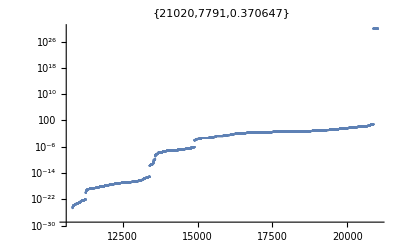

SparseArray[<10199>, {410, 410}]

SparseArray[…]

```mathematica
SetDirectory["C:\\Users\\struther\\Desktop\\2022-23-Classes\\5631\\SampleMatrices"];
fStream=OpenRead["Matrix1.txt"];
(* Skip the Header *)
Skip[fStream,"String",2]
(* Read Dimensions and count *)
{n,m,nz}=Read[fStream,{Number,Number,Number}];
(* Tidy up the end iof the line *)
Skip[fStream,"String"];
(* read the data *)
Y1 = Partition[ReadList[fStream,Number],3]/.{i_,j_,z_}:>{i+1,j+1}->z;
Close[fStream]
(* Purge the Zeros *)
Y1F=Select[Y1, Abs[#⟦2⟧]>2*10^-16 &];
(* inspect nonzero entries and count non-zeros *)
{nnz1,nnzF}=Map[Length,{Y1,Y1F}];
ListLogPlot[Sort[Abs[Y1⟦All,2⟧]],PlotRange->All,
PlotLabel->{nnz1,nnzF, N[nnzF/nnz1]}]
(* Build Sparse Matrices *)
Y1=SparseArray[Y1,{n,m}]
Y1F=SparseArray[Y1F,{n,m}]
(* Dump output as mtx *)
Export["Y1.mtx",Y1];
Export["Y1F.mtx",Y1F];
```

I just learned that Mathematica automatically prunes the “stored” zeros.  Not sure how I feel about that! Here is the spectrum.

```mathematica
NewNorm=Norm[Normal[Y1]/.{1.0000000000000000199`19.*^30->1},"Frobenius"]
```

70.0086

```mathematica
Y1[[1,1]]
```

1.00000000000000002×10^30

```mathematica
SymTest=Norm[Y1-Transpose[Y1],"Frobenius"];
λs=Select[Eigenvalues[Normal[Y1]],Norm[#]<10^29&];
Norm[Im[λs]]
TabView[{
"Y1"->MatrixPlot[Y1,PlotLabel->{SymTest,SymTest/NewNorm,SymTest/Norm[Y1,"Frobenius"]},PlotLegends->Automatic],
"Y1-Y1ᵀ"->MatrixPlot[Y1-Transpose[Y1],PlotLabel->{SymTest,SymTest/NewNorm,SymTest/Norm[Y1,"Frobenius"]},
PlotLegends->Automatic],
"λs"->ListPlot[Sort[λs]],
"|λs|"->ListLogPlot[Sort[Abs[λs]]],
"|λs|_(3 : 60)"->ListLogPlot[Sort[Abs[λs]]⟦3;;60⟧],
"|λs|_(61 : end)"->ListLogPlot[Sort[Abs[λs]]⟦61;;-1⟧]
}]
```

0

123456

## Matrix 2

Matrix2.txt

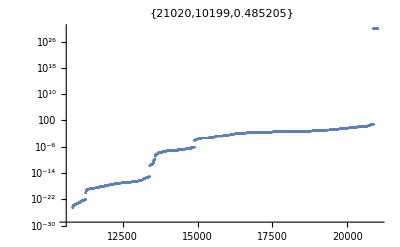

SparseArray[<10199>, {410, 410}]

SparseArray[<10199>, {410, 410}]

```mathematica
SetDirectory["C:\\Users\\struther\\Desktop\\2022-23-Classes\\5631\\SampleMatrices"];
fStream=OpenRead["Matrix2.txt"];
(* Skip the Header *)
Skip[fStream,"String",2]
(* Read Dimensions and count *)
{n,m,nz}=Read[fStream,{Number,Number,Number}];
(* Tidy up the end iof the line *)
Skip[fStream,"String"];
(* read the data *)
Y2 = Partition[ReadList[fStream,Number],3]/.{i_,j_,z_}:>{i+1,j+1}->z;
Close[fStream]
(* Purge the Zeros *)
Y2F=Select[Y2, Abs[#⟦2⟧]>0 &];
(* inspect nonzero entries and count non-zeros *)
{nnz1,nnzF}=Map[Length,{Y2,Y2F}];
ListLogPlot[Sort[Abs[Y2⟦All,2⟧]],PlotRange->All,
PlotLabel->{nnz1,nnzF, N[nnzF/nnz1]}]
(* Build Sparse Matrices *)
Y2=SparseArray[Y2,{n,m}]
Y2F=SparseArray[Y2F,{n,m}]
(* Dump output as mtx *)
Export["Y2.mtx",Y1];
Export["Y2F.mtx",Y1F];
```

I just learned that Mathematica automatically prunes the “stored” zeros.  Not sure how I feel about that! Here is the spectrum.

```mathematica
SymTest=Norm[Y2-Transpose[Y2],"Frobenius"];
λs=Select[Eigenvalues[Normal[Y2]],Norm[#]<10^29&];
Norm[Im[λs]]
TabView[{
"Y2"->MatrixPlot[Y1,PlotLabel->{SymTest,SymTest/Norm[Y2,"Frobenius"]},PlotLegends->Automatic],
"Y2-Y2ᵀ"->MatrixPlot[Y2-Transpose[Y1],PlotLabel->{SymTest,SymTest/Norm[Y1,"Frobenius"]},PlotLegends->Automatic],
"λs"->ListPlot[Sort[λs]],
"|λs|"->ListLogPlot[Sort[Abs[λs]]],
"|λs|_(3 : 60)"->ListLogPlot[Sort[Abs[λs]]⟦3;;60⟧],
"|λs|_(61 : end)"->ListLogPlot[Sort[Abs[λs]]⟦61;;-1⟧]
}]
```

0

123456

## Diagonal Jacobi Preconditioner

```mathematica
Normal[Diagonal[Y1]]
```

{1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,0,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,0,0.8019170370957904304,0.8019170370957904304,0.01111111111111110286,0.01111111111111110286,0.6798140734153428344,0.6798140734153428344,0.009259259247876424834,0.009259259247876424834,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,0,0.6941518520428011652,0.6941518520428011652,0.009259259259259258745,0.009259259259259258745,0.567269630479310116,0.567269630479310116,0.007407407418790236398,0.007407407418790236398,0.6355286403525868266,0.6355286403525868266,0.008641975282082039675,0.008641975282082039675,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,0,0.6355286403966518005,0.6355286403966518005,0.008641975282082036206,0.008641975282082036206,0.5529318528378748265,0.5529318528378748265,0.00740740742258451032,0.00740740742258451032,0.2476744446318996651,0.2476744446318996651,0.002777777779200630171,0.002777777779200630171,1.388888889600315696×10^-11,0,0.5816074071640986443,0.5816074071640986443,0.00740740739981885638,0.00740740739981885638,0.5672696295226637986,0.5672696295226637986,0.0074074074036131329,0.0074074074036131329,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,0,0.5529318523007979991,0.5529318523007979991,0.007407407414995957271,0.007407407414995957271,0.5529318518959172035,0.5529318518959172035,0.007407407407407410292,0.007407407407407410292,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,0.567269628073005627,0.567269628073005627,0.00740740738084747028,0.00740740738084747028,0.8019170356877497463,0.8019170356877497463,0.01111111108834544892,0.01111111108834544892,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,0,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,0,0.6941518496193599397,0.6941518496193599397,0.009259259221316490027,0.009259259221316490027,0.532530833193806896,0.532530833193806896,0.007291666663109527824,0.007291666663109527824,3.64583333155476675×10^-11,0,0.8060988894443260611,0.8060988894443260611,0.01111111111869966459,0.01111111111869966459,1.185030618214892417,1.185030618214892417,0.01728395063246105853,0.01728395063246105853,1.02879814724291152,1.02879814724291152,0.0148148147996377128,0.0148148147996377128,1.185030618214892639,1.185030618214892639,0.017283950632461062,0.017283950632461062,0.8060988894443263941,0.8060988894443263941,0.01111111111869966805,0.01111111111869966805,0.4658641663229824426,0.4658641663229824426,0.006249999993597155079,0.006249999993597155079,3.124999996798579226×10^-11,0,0.58160740614869888,0.58160740614869888,0.00740740738464175201,0.00740740738464175201,0.4254522224594289859,0.4254522224594289859,0.005555555558401262944,0.005555555558401262944,2.777777779200633007×10^-11,0,0.8060988894443268382,0.8060988894443268382,0.01111111111869967499,0.01111111111869967499,1.03059037223225447,1.03059037223225447,0.01481481484516903625,0.01481481484516903625,0.5672696290296523891,0.5672696290296523891,0.00740740739602458332,0.00740740739602458332,0.679814076096780795,0.679814076096780795,0.009259259293407744867,0.009259259293407744867,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,0.581607407915107788,0.581607407915107788,0.007407407414995965944,0.007407407414995965944,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,0,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,0,0.3143411115609159867,0.3143411115609159867,0.003819444451558712261,0.003819444451558712261,1.909722225779356464×10^-11,0,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,0.8019170383863239993,0.8019170383863239993,0.01111111113387676201,0.01111111113387676201,0.6941518540843434337,0.6941518540843434337,0.009259259297202023994,0.009259259297202023994,0.3143411103741695079,0.3143411103741695079,0.003819444431638758554,0.003819444431638758554,1.909722215819380044×10^-11,0,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,0.6798140720513672353,0.6798140720513672353,0.009259259225110769154,0.009259259225110769154,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,0,0.5672696284925751176,0.5672696284925751176,0.007407407388436023331,0.007407407388436023331,0.552931850416881976,0.552931850416881976,0.007407407384641745071,0.007407407384641745071,0.5529318498357402856,0.5529318498357402856,0.007407407377053195491,0.007407407377053195491,1.185030618214892861,1.185030618214892861,0.01728395063246106894,0.01728395063246106894,1.185030618214892861,1.185030618214892861,0.01728395063246106894,0.01728395063246106894,0.6544242599271706817,0.6544242599271706817,0.009259259270642087453,0.009259259270642087453,4.62962963532104629×10^-11,0,1.03059037223225447,1.03059037223225447,0.01481481484516903799,0.01481481484516903799,0.4254522220511132158,0.4254522220511132158,0.005555555552709847723,0.005555555552709847723,2.77777777635492523×10^-11,0,0.5672696279995638191,0.5672696279995638191,0.007407407380847474618,0.007407407380847474618,0.8060988894443267272,0.8060988894443267272,0.01111111111869967152,0.01111111111869967152,0.6355286435539646561,0.6355286435539646561,0.008641975335201904085,0.008641975335201904085,1.028798149053385069,1.028798149053385069,0.0148148148299919215,0.0148148148299919215,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,0.4658641672117542765,0.4658641672117542765,0.006250000009248545853,0.006250000009248545853,3.125000004624275215×10^-11,0,0.567269631186253287,0.567269631186253287,0.007407407433967339028,0.007407407433967339028,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,0,0.5529318498798054815,0.5529318498798054815,0.007407407377053192889,0.007407407377053192889,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,0,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,0.6798140734153428344,0.6798140734153428344,0.009259259247876428303,0.009259259247876428303,0.6941518520428009431,0.6941518520428009431,0.009259259259259255276,0.009259259259259255276,0.6355286435980302962,0.6355286435980302962,0.008641975335201907554,0.008641975335201907554,0.567269630479310116,0.567269630479310116,0.007407407418790236398,0.007407407418790236398,0.3143411107356659517,0.3143411107356659517,0.003819444437330172908,0.003819444437330172908,1.909722218665087501×10^-11,0,0.4658641671067432766,0.4658641671067432766,0.006250000006402838676,0.006250000006402838676,3.12500000320142181×10^-11,0,0.5816074071640986443,0.5816074071640986443,0.00740740739981885638,0.00740740739981885638,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,0,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,0,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,0.801917037095790652,0.801917037095790652,0.01111111111111110807,0.01111111111111110807,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,0,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,1.00000000000000002×10^30,0}